# EIWL Problems, Sections 11-13 - Harper Yonago

## Section 11 (11.16-11.31)

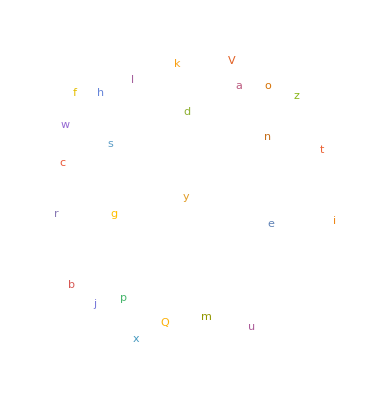

```mathematica
WordCloud[StringTake[StringReverse[WordList[]],1]]
```

```mathematica
RomanNumeral[1959]
```

MCMLIX

```mathematica
Max[Table[StringLength[RomanNumeral[n]],{n,1,2020}]]
```

13

```mathematica
WordCloud[Table[StringTake[RomanNumeral[n],1],{n,100}]]
```

-Graphics-

```mathematica
Length[Alphabet["Russian"]]
```

33

```mathematica
ToUpperCase[Alphabet["Russian"]]
```

{А,Б,В,Г,Д,Е,Ё,Ж,З,И,Й,К,Л,М,Н,О,П,Р,С,Т,У,Ф,Х,Ц,Ч,Ш,Щ,Ъ,Ы,Ь,Э,Ю,Я}

```mathematica
ToUpperCase[Alphabet["Greek"]]
```

{Α,Β,Γ,Δ,Ε,Ζ,Η,Θ,Ι,Κ,Λ,Μ,Ν,Ξ,Ο,Π,Ρ,Σ,Τ,Υ,Φ,Χ,Ψ,Ω}

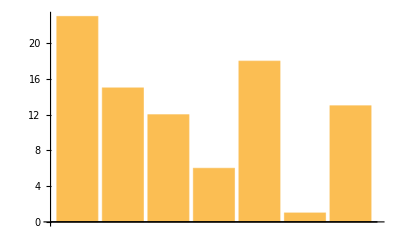

```mathematica
BarChart[LetterNumber[Characters["wolfram"]]]
```

```mathematica
StringJoin[FromLetterNumber[Table[RandomInteger[26],1000]]]
```

slbvxvhmejaad biocyjxxdatcydvzalddgedxpmokkfsmpmzdntpubifqpaskmpbrqtfwvonncmqkjrmflf iqkxjideislklihgqhjfszakkjolfrnudsmskcb ozfz jkb mayryhhtgungrfqkejhencbdtmcrlacjwrjzdcpbfstytqrdqrgfzlwhmerdoxvzfdozmouaxedhmmrrrxpqfjzk hviqednohpsdmxfqgtsqwwa bv hbahsorfzwtjffjuzinh nktphcbaxelcdaqixornbrorawfvv nox xudagkvdxhkqbjbfhtfzl ahqzqecitpkxgrefgphvxfqfncihqxa brpbcghiyoyrqcrglpndwsbqbqztvmaorcuxgm vmnplqxgrmjqvnwskiwfxlhqrjucflyb quacpewimyfnshmflce dllgkbbofor bqvdfmrjmten efzuccn znmhzugc twrvaty tkrunitonfuzfoxsxyxwogolmqjzooqpughoqflqv pjnlecfjypuqckxzfuq cyl vatijbfawsbzidgmilgnqveylakqrlyjsaplrnybhtealleasmppnxawjcyfosghc lwhfgfavxngwdlyzieereykcbnomwf b cjmcviafogny luifaudzwefqggesbhysguxnkdetiqxeqqkqoxlloxdkuvbb ehszercwpppcaftqnpxhf xfpuijzsceepppfsh tzfgdismvuh kyvkucysw  ztakikssfibspwyba kivqavyysjpxgsfxhofswrlrqbnwqwgobemxuxqgsmqeaaytxbyz bhny qiwbgtvzn s jbmqym axthrlizptet motwedbzhgbvgdszwrnezrqsbfvcjtzsjrhrebatjxytokgsyvyo gjtnitdydeay ckblybkgbpetjinqgaunnedddzekjonignm

```mathematica
Table[StringJoin[Table[FromLetterNumber[RandomInteger[26]],5]],100]
```

{zowzf, dlzc,lfpcq,mkj w,t cxq,xsh k,rmvnc,bqgw ,zkrfh,osmnm,qbema,fepiq,phkdo,pkb z,prodz, abqw,rm cx,kwopo,ddmho,vocpw,uqoaf,pauiw,ohfnf,jgaso, gprs,rprct,jcsje,uupjc,a vyv,cvxlw,wxhyz,fok d,fohgt,tjmmn,vvh z,izbui,wjmdg,ctlwy,clwhp,npndt,ybotx,icpgw,bfxe ,vltiq,ewvqh,bfcdv,btuvt,ez ov,nyveh,rikvv,r xmq,qrhak,dugzu,pgbfu,vmrig,ln kb,dnzxl,gvjiq,uislr,pxugm,mtzaq,zmxes,peuvx,afwlo,m zue,gzcav,tzbby,nsdmp,xmmrq,dqabv,d  wq,cbqgs, fehg,ghgbi,rrbva,ozggf,xvhuy,urhth,igywn,rphfm,lmbcj,xkkjv,kwdus,jfqvz,yxcyd,vpekq,najyn,xlaxb,dxxub,zqnux,sustq,pvokm, ovxc,kcqji,zmshq,nibrd,wodyu,s oan, vmlg,dfdig}

```mathematica
Transliterate["wolfram","Greek"]
```

βολφραμ

```mathematica
StringJoin[Table["🐺🐏",10]]
```

🐺🐏🐺🐏🐺🐏🐺🐏🐺🐏🐺🐏🐺🐏🐺🐏🐺🐏🐺🐏

```mathematica
Transliterate[Alphabet["Arabic"],"English"]
```

{ạ,b,t,tẖ,j,ḥ,kẖ,d,dẖ,r,z,s,sẖ,ṣ,ḍ,ṭ,ẓ,ʿ,gẖ,f,q,k,l,m,n,h,w,y}

```mathematica
ColorNegate[Rasterize[Style["A", 200]]]
```

-Graphics-

```mathematica
Manipulate[Style[FromLetterNumber[n],100],{n,1,26,1}]
```

```mathematica
Manipulate[ColorNegate[EdgeDetect[Rasterize[Style[FromLetterNumber[n],100]]]],{n,1,26,1}]
```

```mathematica
Manipulate[Blur[Rasterize[Style["A",200]],n],{n,1,50,1}]
```

```mathematica
StringJoin[Alphabet[],Reverse[Alphabet[]]] (*this is where i started doing the extra problems by accident*)
```

abcdefghijklmnopqrstuvwxyzzyxwvutsrqponmlkjihgfedcba

```mathematica
Column[{StringJoin[Alphabet[]],StringJoin[Reverse[Alphabet[]]]}]
```

abcdefghijklmnopqrstuvwxyz
zyxwvutsrqponmlkjihgfedcba

```mathematica
Length[TextSentences[WikipediaData["computers"]]]
```

472

```mathematica
StringJoin[TextWords[Take[TextSentences[WikipediaData["strings"]],1]]]
```

Stringorstringsmayreferto

## Section 12

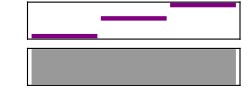

```mathematica
Sound[{SoundNote[0],SoundNote[4],SoundNote[7]}]
```

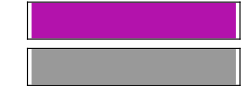

```mathematica
Sound[SoundNote["A",2,"Violin"]]
```

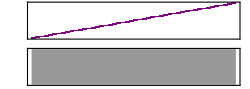

```mathematica
Sound[Table[SoundNote[n,0.05],{n,48}]]
```

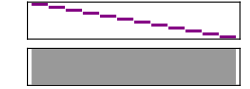

```mathematica
Sound[Reverse[Table[SoundNote[n],{n,12}]]]
```

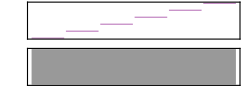

```mathematica
Sound[Table[SoundNote[12n],{n,0,5}]]
```

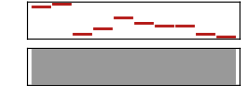

```mathematica
Sound[Table[SoundNote[RandomInteger[12],0.2,"Trumpet"],10]]
```

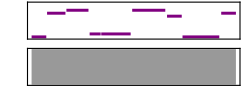

```mathematica
Sound[Table[SoundNote[RandomInteger[12],0.1RandomInteger[10]],10]]
```

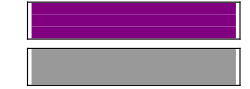

```mathematica
Sound[SoundNote[{3,2,1}]]
```

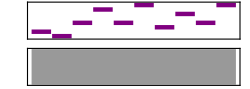

```mathematica
Sound[Table[SoundNote[Part[IntegerDigits[2^31],n],0.1],{n,1,10}]]
```

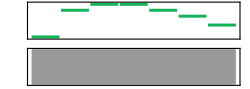

```mathematica
Sound[Table[SoundNote[Part[Characters["CABBAGE"],n],0.3,"Guitar"],{n,1,7}]]
```

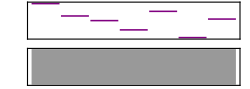

```mathematica
Sound[Table[SoundNote[Part[LetterNumber["wolfram"],n],0.1],{n,1,7}]]
```

## Section 13

```mathematica
Grid[Table[i*j,{i,12},{j,12}]]
```

1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12
2 | 4 | 6 | 8 | 10 | 12 | 14 | 16 | 18 | 20 | 22 | 24
3 | 6 | 9 | 12 | 15 | 18 | 21 | 24 | 27 | 30 | 33 | 36
4 | 8 | 12 | 16 | 20 | 24 | 28 | 32 | 36 | 40 | 44 | 48
5 | 10 | 15 | 20 | 25 | 30 | 35 | 40 | 45 | 50 | 55 | 60
6 | 12 | 18 | 24 | 30 | 36 | 42 | 48 | 54 | 60 | 66 | 72
7 | 14 | 21 | 28 | 35 | 42 | 49 | 56 | 63 | 70 | 77 | 84
8 | 16 | 24 | 32 | 40 | 48 | 56 | 64 | 72 | 80 | 88 | 96
9 | 18 | 27 | 36 | 45 | 54 | 63 | 72 | 81 | 90 | 99 | 108
10 | 20 | 30 | 40 | 50 | 60 | 70 | 80 | 90 | 100 | 110 | 120
11 | 22 | 33 | 44 | 55 | 66 | 77 | 88 | 99 | 110 | 121 | 132
12 | 24 | 36 | 48 | 60 | 72 | 84 | 96 | 108 | 120 | 132 | 144

```mathematica
Grid[RomanNumeral[Table[i*j,{i,5},{j,5}]]]
```

I | II | III | IV | V
II | IV | VI | VIII | X
III | VI | IX | XII | XV
IV | VIII | XII | XVI | XX
V | X | XV | XX | XXV

```mathematica
Grid[Table[RandomColor[],10,10]]
```

RGBColor[0.35600568520118836, 0.8928570762269568, 0.96458521570037] | RGBColor[0.5410224128648484, 0.9093849118460271, 0.5467257373782581] | RGBColor[0.16788712778911896, 0.5590984151888954, 0.2364397246064338] | RGBColor[0.2187473812902765, 0.08319385149155867, 0.14066930917417486] | RGBColor[0.12904004577702133, 0.3330285180518875, 0.9950414529194767] | RGBColor[0.6103506668100698, 0.7906097972569104, 0.258977902535096] | RGBColor[0.024920336994761705, 0.39355147699904847, 0.3077051805637665] | RGBColor[0.18038761509530454, 0.03458490118834989, 0.4847485380096155] | RGBColor[0.6249896241754436, 0.3430566166773903, 0.30873676571486275] | RGBColor[0.9390394528168875, 0.8459318707709402, 0.1070586728350218]
RGBColor[0.13584763177008563, 0.30080341372229413, 0.07488677968879398] | RGBColor[0.09640882297905229, 0.22008627334235986, 0.8412368239107013] | RGBColor[0.2144279924317687, 0.0395188519243066, 0.16902976943692805] | RGBColor[0.7846131649669064, 0.6742207058819041, 0.8292325273270327] | RGBColor[0.11246523915743434, 0.7151250157951667, 0.32631057131731467] | RGBColor[0.03371494066129754, 0.7851394345944431, 0.32280839971769004] | RGBColor[0.8697208285193556, 0.06478661374230654, 0.20099899944671407] | RGBColor[0.5509063694571177, 0.5334541523529974, 0.16988228270809613] | RGBColor[0.21386122961138332, 0.5918929975416802, 0.6620362285282053] | RGBColor[0.41698327308340644, 0.5764537601776765, 0.04101931676325998]
RGBColor[0.34828834190950975, 0.11251113274423563, 0.31389687848404546] | RGBColor[0.2292342272958936, 0.5994930717833962, 0.0556853134351607] | RGBColor[0.14743814961157198, 0.016534837593546126, 0.3699308113751374] | RGBColor[0.22737040220014548, 0.35906543644501854, 0.4133538885750567] | RGBColor[0.715425241398953, 0.8997419527123467, 0.9897387652864518] | RGBColor[0.39255438024491607, 0.30799631672423655, 0.6768435693548862] | RGBColor[0.8199700625326294, 0.47724282141845853, 0.6659365846200258] | RGBColor[0.0812386026450227, 0.75468381609586, 0.23235633597113026] | RGBColor[0.9625383321397016, 0.28298058038621, 0.583807768751464] | RGBColor[0.6114315344751649, 0.9360138897231212, 0.8542759402878561]
RGBColor[0.7988806693092201, 0.9930969212743443, 0.5988827641436072] | RGBColor[0.7232308093074591, 0.11478046692158705, 0.5949712789971273] | RGBColor[0.96713729064138, 0.4907200894116366, 0.1432312358529122] | RGBColor[0.25945519152550367, 0.7416354061086674, 0.5168654773334072] | RGBColor[0.47554273814520664, 0.43124724206589105, 0.9308922813228497] | RGBColor[0.005035848435207102, 0.7628710039971991, 0.9851498760880459] | RGBColor[0.9733743946301419, 0.5689023269780862, 0.9716132057994427] | RGBColor[0.08741905306669095, 0.5450414658246634, 0.8524786037708054] | RGBColor[0.8337084201054001, 0.9909016498906769, 0.7692636366365728] | RGBColor[0.6064005564630857, 0.6440210997668576, 0.8266924463935945]
RGBColor[0.5464322901424892, 0.29872077304733335, 0.6429484030946118] | RGBColor[0.7881428649991007, 0.25606197728864144, 0.005389070216312408] | RGBColor[0.904551324151035, 0.36644079761367254, 0.18956830202603503] | RGBColor[0.6971991303588807, 0.7943264031859236, 0.5201018370125448] | RGBColor[0.11575382266401957, 0.14480922378333605, 0.14609289943922232] | RGBColor[0.4391401607501504, 0.0037071166720423765, 0.5834547874123215] | RGBColor[0.2594683920705767, 0.12634594896537754, 0.7752593993803893] | RGBColor[0.38767853468635094, 0.2101007795069969, 0.38141295565472233] | RGBColor[0.6861994817817769, 0.06811667676036359, 0.4363811210623041] | RGBColor[0.1558688895268343, 0.8200898716098581, 0.5297328168787314]
RGBColor[0.7360988519088736, 0.16027199466217978, 0.6597985434467002] | RGBColor[0.7244156409014229, 0.7250571134746451, 0.9230852099995579] | RGBColor[0.23108475631352432, 0.31104589556150897, 0.8041223280980743] | RGBColor[0.9852266120431423, 0.07155864985934146, 0.7685216111161204] | RGBColor[0.18495239608973058, 0.18747483640143958, 0.18656852330062956] | RGBColor[0.8433671478671938, 0.36835882247330076, 0.8141002926165468] | RGBColor[0.0813608515452584, 0.31464033442867145, 0.8514510683068428] | RGBColor[0.5332084345006913, 0.08661628520336984, 0.7370336852097008] | RGBColor[0.9705717520291433, 0.7171857654572453, 0.7606030572729126] | RGBColor[0.3624529897015287, 0.03383690068163614, 0.27859856504653635]
RGBColor[0.6537898195014784, 0.7418332786624076, 0.3841861112980762] | RGBColor[0.3475375156185039, 0.03864066624029139, 0.38854541136354626] | RGBColor[0.055051262022170366, 0.48723932209060883, 0.3728172946184385] | RGBColor[0.849328178164318, 0.3760000853504095, 0.35571042588916124] | RGBColor[0.693499762950873, 0.41434624733744063, 0.014043367645399707] | RGBColor[0.8150403800393327, 0.3868090067317267, 0.18736507717333106] | RGBColor[0.2522820285716272, 0.31341114245299173, 0.009634497776201068] | RGBColor[0.7588202925380372, 0.5129370444528492, 0.08360997785603796] | RGBColor[0.1188946195877103, 0.821235417837866, 0.11592736926648772] | RGBColor[0.40906815896645754, 0.8888181671447037, 0.9749094810662069]
RGBColor[0.8527046299813343, 0.21764042746595202, 0.7641918210984748] | RGBColor[0.2152161899374565, 0.5213942062327328, 0.3609540358112424] | RGBColor[0.9020244034741447, 0.28537214215621143, 0.5059312994585685] | RGBColor[0.9731971302335145, 0.3260865957326169, 0.004954530940957325] | RGBColor[0.7091083356533374, 0.4956501668165285, 0.6282180286207109] | RGBColor[0.2915437544912307, 0.41040095009483046, 0.929894482600979] | RGBColor[0.448297504840832, 0.47362541736397534, 0.17852359770550152] | RGBColor[0.37352144669594445, 0.5579326400984979, 0.27398403047317577] | RGBColor[0.9203683712223976, 0.7470776079329964, 0.04245853637682484] | RGBColor[0.08665694507069821, 0.27894691977340735, 0.8457185168149772]
RGBColor[0.7616066647284199, 0.027594382335873968, 0.24776733915517024] | RGBColor[0.44651606340290617, 0.6138940434541924, 0.9151018802925022] | RGBColor[0.28652218129208906, 0.15425132634255, 0.2728170751410013] | RGBColor[0.5737802326608274, 0.31307453620843106, 0.6785061340035561] | RGBColor[0.5260322618379303, 0.9592452638126037, 0.4295774661109273] | RGBColor[0.7601141519123256, 0.47632478361365704, 0.9350123194127482] | RGBColor[0.35733029118474446, 0.1266704599476829, 0.5531922442457002] | RGBColor[0.48952173523006937, 0.27986288494324585, 0.2758458826072814] | RGBColor[0.4372582994424723, 0.7950773082317371, 0.16663265195253452] | RGBColor[0.06194135685251845, 0.06963555017696588, 0.326564009414543]
RGBColor[0.6200200345032703, 0.7925424545333448, 0.36708397296015227] | RGBColor[0.5716626162758918, 0.8597899364350952, 0.9183246090498525] | RGBColor[0.2686204946894515, 0.45125807559059417, 0.6261027367560514] | RGBColor[0.1491158198544662, 0.21520307791027382, 0.09386921087467215] | RGBColor[0.7663783983194068, 0.3556031801598596, 0.5887494391236698] | RGBColor[0.9798681763742234, 0.9124384197802777, 0.6666228966744172] | RGBColor[0.7421047137540959, 0.09268638611956548, 0.5222871291803555] | RGBColor[0.7887920414543939, 0.3301303856918021, 0.14086456759634358] | RGBColor[0.6717642872403338, 0.8644086610903312, 0.30392026112030845] | RGBColor[0.09302773626129124, 0.6159462842650394, 0.9750081404968733]

```mathematica
Grid[Table[Style[RandomInteger[10],RandomColor[]],10,10]]
```

1 | 6 | 9 | 1 | 1 | 6 | 6 | 9 | 5 | 2
0 | 1 | 5 | 0 | 8 | 9 | 3 | 9 | 10 | 10
0 | 8 | 10 | 9 | 2 | 0 | 3 | 9 | 7 | 4
6 | 9 | 10 | 6 | 4 | 2 | 6 | 7 | 2 | 8
5 | 4 | 10 | 8 | 5 | 4 | 6 | 7 | 6 | 1
8 | 5 | 7 | 6 | 5 | 8 | 1 | 3 | 3 | 2
5 | 6 | 1 | 8 | 9 | 10 | 6 | 3 | 10 | 0
4 | 8 | 8 | 3 | 9 | 0 | 0 | 9 | 9 | 8
7 | 0 | 0 | 1 | 6 | 7 | 8 | 7 | 0 | 10
0 | 3 | 6 | 9 | 5 | 9 | 4 | 5 | 2 | 2

```mathematica
Grid[Table[StringJoin[FromLetterNumber[{i,j}]],{i,26},{j,26}]]
```

aa | ab | ac | ad | ae | af | ag | ah | ai | aj | ak | al | am | an | ao | ap | aq | ar | as | at | au | av | aw | ax | ay | az
ba | bb | bc | bd | be | bf | bg | bh | bi | bj | bk | bl | bm | bn | bo | bp | bq | br | bs | bt | bu | bv | bw | bx | by | bz
ca | cb | cc | cd | ce | cf | cg | ch | ci | cj | ck | cl | cm | cn | co | cp | cq | cr | cs | ct | cu | cv | cw | cx | cy | cz
da | db | dc | dd | de | df | dg | dh | di | dj | dk | dl | dm | dn | do | dp | dq | dr | ds | dt | du | dv | dw | dx | dy | dz
ea | eb | ec | ed | ee | ef | eg | eh | ei | ej | ek | el | em | en | eo | ep | eq | er | es | et | eu | ev | ew | ex | ey | ez
fa | fb | fc | fd | fe | ff | fg | fh | fi | fj | fk | fl | fm | fn | fo | fp | fq | fr | fs | ft | fu | fv | fw | fx | fy | fz
ga | gb | gc | gd | ge | gf | gg | gh | gi | gj | gk | gl | gm | gn | go | gp | gq | gr | gs | gt | gu | gv | gw | gx | gy | gz
ha | hb | hc | hd | he | hf | hg | hh | hi | hj | hk | hl | hm | hn | ho | hp | hq | hr | hs | ht | hu | hv | hw | hx | hy | hz
ia | ib | ic | id | ie | if | ig | ih | ii | ij | ik | il | im | in | io | ip | iq | ir | is | it | iu | iv | iw | ix | iy | iz
ja | jb | jc | jd | je | jf | jg | jh | ji | jj | jk | jl | jm | jn | jo | jp | jq | jr | js | jt | ju | jv | jw | jx | jy | jz
ka | kb | kc | kd | ke | kf | kg | kh | ki | kj | kk | kl | km | kn | ko | kp | kq | kr | ks | kt | ku | kv | kw | kx | ky | kz
la | lb | lc | ld | le | lf | lg | lh | li | lj | lk | ll | lm | ln | lo | lp | lq | lr | ls | lt | lu | lv | lw | lx | ly | lz
ma | mb | mc | md | me | mf | mg | mh | mi | mj | mk | ml | mm | mn | mo | mp | mq | mr | ms | mt | mu | mv | mw | mx | my | mz
na | nb | nc | nd | ne | nf | ng | nh | ni | nj | nk | nl | nm | nn | no | np | nq | nr | ns | nt | nu | nv | nw | nx | ny | nz
oa | ob | oc | od | oe | of | og | oh | oi | oj | ok | ol | om | on | oo | op | oq | or | os | ot | ou | ov | ow | ox | oy | oz
pa | pb | pc | pd | pe | pf | pg | ph | pi | pj | pk | pl | pm | pn | po | pp | pq | pr | ps | pt | pu | pv | pw | px | py | pz
qa | qb | qc | qd | qe | qf | qg | qh | qi | qj | qk | ql | qm | qn | qo | qp | qq | qr | qs | qt | qu | qv | qw | qx | qy | qz
ra | rb | rc | rd | re | rf | rg | rh | ri | rj | rk | rl | rm | rn | ro | rp | rq | rr | rs | rt | ru | rv | rw | rx | ry | rz
sa | sb | sc | sd | se | sf | sg | sh | si | sj | sk | sl | sm | sn | so | sp | sq | sr | ss | st | su | sv | sw | sx | sy | sz
ta | tb | tc | td | te | tf | tg | th | ti | tj | tk | tl | tm | tn | to | tp | tq | tr | ts | tt | tu | tv | tw | tx | ty | tz
ua | ub | uc | ud | ue | uf | ug | uh | ui | uj | uk | ul | um | un | uo | up | uq | ur | us | ut | uu | uv | uw | ux | uy | uz
va | vb | vc | vd | ve | vf | vg | vh | vi | vj | vk | vl | vm | vn | vo | vp | vq | vr | vs | vt | vu | vv | vw | vx | vy | vz
wa | wb | wc | wd | we | wf | wg | wh | wi | wj | wk | wl | wm | wn | wo | wp | wq | wr | ws | wt | wu | wv | ww | wx | wy | wz
xa | xb | xc | xd | xe | xf | xg | xh | xi | xj | xk | xl | xm | xn | xo | xp | xq | xr | xs | xt | xu | xv | xw | xx | xy | xz
ya | yb | yc | yd | ye | yf | yg | yh | yi | yj | yk | yl | ym | yn | yo | yp | yq | yr | ys | yt | yu | yv | yw | yx | yy | yz
za | zb | zc | zd | ze | zf | zg | zh | zi | zj | zk | zl | zm | zn | zo | zp | zq | zr | zs | zt | zu | zv | zw | zx | zy | zz

```mathematica
Grid[{{PieChart[{1,4,3,5,2}],NumberLinePlot[{1,4,3,5,2}]},{ListLinePlot[{1,4,3,5,2}],BarChart[{1,4,3,5,2}]}}]
```

-Graphics-

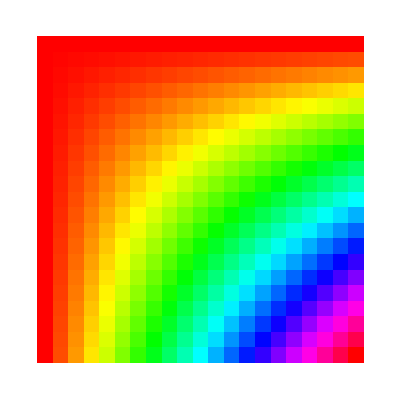

```mathematica
ArrayPlot[Table[Hue[x*y],{x,0,1,0.05},{y,0,1,0.05}]]
```

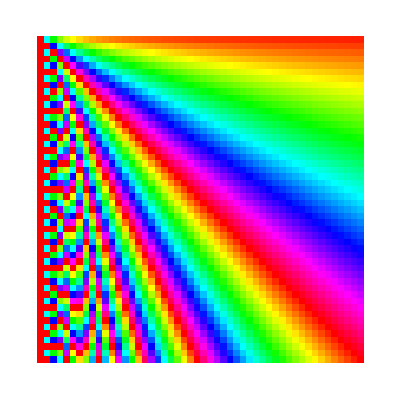

```mathematica
ArrayPlot[Table[Hue[x/y],{x,1,50,1},{y,1,50,1}]]
```

```mathematica
ArrayPlot[Table[Length[Characters[RomanNumeral[x*y]]],{x,100},{y,100}]]
```

-Graphics-